# Bicubic Spline Interpolation

This setup cubic splines and scales them for use in the rays code.

## File

```mathematica
file=SystemDialogInput["FileOpen"]
```

/Users/m4c/VMEC/CTH/wout_cth.vmec.nc

```mathematica
chi=Normal[Import[file,{"Datasets","chi"}]];
phi=Normal[Import[file,{"Datasets","phi"}]];
lmns=Normal[Import[file,{"Datasets","lmns"}]];
rmnc=Normal[Import[file,{"Datasets","rmnc"}]];
zmns=Normal[Import[file,{"Datasets","zmns"}]];
```

```mathematica
ns=Normal[Import[file,{"Datasets","ns"}]];
```

```mathematica
xm=Normal[Import[file,{"Datasets","xm"}]];
xn=Normal[Import[file,{"Datasets","xn"}]];
```

```mathematica
sfull=Subdivide[0.0,1.0,ns-1];
shalf=(sfull[[2;;]]+sfull[[;;-2]])/2;
```

```mathematica
ds=sfull[[2]]-sfull[[1]];
```

## Cubic Spline

```mathematica
m[n_]:=Table[If[i==j,If[i==1||i==n,2,4],If[i==j-1||i==j+1,1,0]],{i,n},{j,n}];
```

```mathematica
b[a_][n_]:=Table[3*(a[[Min[i+1,n]]]-a[[Max[i-1,1]]]),{i,n}];
```

```mathematica
d[a_]:=LinearSolve[m[Length[a]],b[a][Length[a]]];
```

```mathematica
c1D[a_]:=Module[{ds,c0,c1,c2,c3,i},
ds=d[a];
c0=a[[;;-2]];
c1=ds[[;;-2]];
c2=3*(a[[2;;]]-a[[;;-2]])-2*ds[[;;-2]]-ds[[2;;]];
c3=2*(a[[;;-2]]-a[[2;;]])+ds[[;;-2]]+ds[[2;;]];
i=Table[i-1,{i,Length[c0]}];
{
c0-c1*i+c2*i*i-c3*i*i*i,
c1-2*c2*i+3*c3*i*i,
c2-3c3*i,
c3
}
]
```

```mathematica
f[dx_][a_][xmin_][x_]:=Module[{ilow,xnorm,result,c0,c1,c2,c3},
ilow=Max[Min[Floor[(x-xmin)/dx]+1,Length[a]-1],1];
xnorm=(x-xmin)/dx;
{c0,c1,c2,c3}=c1D[a];
result=c0[[ilow]]+c1[[ilow]]*xnorm+c2[[ilow]]*xnorm*xnorm+c3[[ilow]]*xnorm*xnorm*xnorm;
{x,ilow,xnorm,result}
];
```

```mathematica
df[dx_][a_][xmin_][x_]:=Module[{ilow,xnorm,result,c0,c1,c2,c3},
ilow=Max[Min[Floor[(x-xmin)/dx]+1,Length[a]-1],1];
xnorm=(x-xmin)/dx;
{c0,c1,c2,c3}=c1D[a];
result=(c1[[ilow]]+2*c2[[ilow]]*xnorm+3*c3[[ilow]]*xnorm*xnorm);
{x,ilow,xnorm,result}
];
```

```mathematica
chic=c1D[Join[Reverse[-chi[[2;;]]],chi]];
phic=c1D[Join[Reverse[-phi[[2;;]]],phi]];
```

```mathematica
rmncc=ParallelTable[c1D[Join[Reverse[If[Mod[xm[[mn]],2]==0,1,-1]*rmnc[[2;;,mn]]],rmnc[[;;,mn]]]],{mn,Length[xm]}];
zmnsc=ParallelTable[c1D[Join[Reverse[If[Mod[xm[[mn]],2]==0,1,-1]*zmns[[2;;,mn]]],zmns[[;;,mn]]]],{mn,Length[xm]}];
```

```mathematica
lmnsc=ParallelTable[c1D[Join[Reverse[If[Mod[xm[[mn]],2]==0,1,-1]*lmns[[2;;,mn]]],lmns[[2;;,mn]]]],{mn,Length[xm]}];
```

```mathematica
sminf=-Last[sfull]
sminh=-Last[shalf]
```

-1.

-0.994949

```mathematica
Dimensions[rmncc[[;;,1,;;]]]
```

{86,198}

```mathematica
Export["vmec.nc",{
"Dimensions"->{
"numsf"->2ns-2,
"numsh"->2ns-3,
"nummn"->Length[rmnc[[1]]]
},
"Datasets"->{
"sminf"->{"Data"->sminf},
"sminh"->{"Data"->sminh},
"ds"->{"Data"->ds},
"xm"->{"Data"->xm, "DimensionNames"->"nummn"},
"xn"->{"Data"->xn, "DimensionNames"->"nummn"},
"chi_c0"->{"Data"->chic[[1]],"DimensionNames"->"numsf"},
"chi_c1"->{"Data"->chic[[2]],"DimensionNames"->"numsf"},
"chi_c2"->{"Data"->chic[[3]],"DimensionNames"->"numsf"},
"chi_c3"->{"Data"->chic[[4]],"DimensionNames"->"numsf"},
"phi_c0"->{"Data"->phic[[1]],"DimensionNames"->"numsf"},
"phi_c1"->{"Data"->phic[[2]],"DimensionNames"->"numsf"},
"rmnc_c0"->{"Data"->rmncc[[;;,1,;;]],"DimensionNames"->{"nummn","numsf"}},
"rmnc_c1"->{"Data"->rmncc[[;;,2,;;]],"DimensionNames"->{"nummn","numsf"}},
"rmnc_c2"->{"Data"->rmncc[[;;,3,;;]],"DimensionNames"->{"nummn","numsf"}},
"rmnc_c3"->{"Data"->rmncc[[;;,4,;;]],"DimensionNames"->{"nummn","numsf"}},
"zmns_c0"->{"Data"->zmnsc[[;;,1,;;]],"DimensionNames"->{"nummn","numsf"}},
"zmns_c1"->{"Data"->zmnsc[[;;,2,;;]],"DimensionNames"->{"nummn","numsf"}},
"zmns_c2"->{"Data"->zmnsc[[;;,3,;;]],"DimensionNames"->{"nummn","numsf"}},
"zmns_c3"->{"Data"->zmnsc[[;;,4,;;]],"DimensionNames"->{"nummn","numsf"}},
"lmns_c0"->{"Data"->lmnsc[[;;,1,;;]],"DimensionNames"->{"nummn","numsh"}},
"lmns_c1"->{"Data"->lmnsc[[;;,2,;;]],"DimensionNames"->{"nummn","numsh"}},
"lmns_c2"->{"Data"->lmnsc[[;;,3,;;]],"DimensionNames"->{"nummn","numsh"}},
"lmns_c3"->{"Data"->lmnsc[[;;,4,;;]],"DimensionNames"->{"nummn","numsh"}}
}},"Rules"]
```

vmec.nc

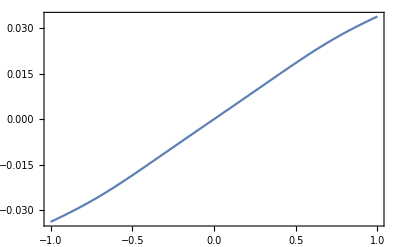

```mathematica
Plot[f[ds][Join[Reverse[-chi[[2;;]]],chi]][sminf][s][[4]],{s,-1,1},PlotRange->Full,Frame->True]
```

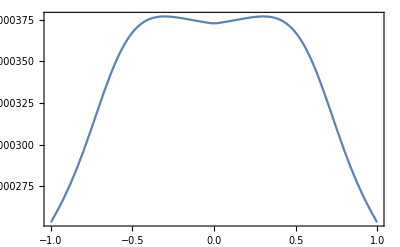

```mathematica
Plot[df[ds][Join[Reverse[-chi[[2;;]]],chi]][sminf][s][[4]],{s,-1,1},PlotRange->Full,Frame->True]
```